## Load the package

```mathematica
<<TRQS`
```

Package TRQS version 0.2.0 (last modification: 07/05/2012).

INFO: Using Quantis as a source of randomness.

Note: You should configure this backend with QuantisSetDevice function by providing information about the type and id of the used Quantis device.

Note: By default the package will use a USB Quantis device with id set to 0.

## Setup used backend (Quantis)

```mathematica
?QuantisSetDevice
```

QuantisSetDevice[type, id] sets the type and the id of the used Quantis device. See also: QuantisSetDeviceType and QuantisSetDeviceId.

```mathematica
QuantisSetDevice["USB",0] (* provide information about the used device - by default the package will use USB device number 0 *)
```

Using Quantis device: type=USB, id=0

## Review libQuantis configuration

```mathematica
QuantisGetLibVersion[]
```

2.5

```mathematica
QuantisGetSerialNumber[]
```

080259A410

## Integer numbers

```mathematica
?TrueRandomInteger
```

TrueRandomInteger[{i_min,i_max}] returns a random integer in the range [i_min,i_max].
TrueRandomInteger[{i_min, i_max}, dim] returns a list of random integers in the range [i_min, i_max] with dim elements.
TrueRandomInteger[i] returns a random integer in the range [0,i].
TrueRandomInteger[] returns 0 or 1.

```mathematica
{TrueRandomInteger[],TrueRandomInteger[10],TrueRandomInteger[{10,20}], TrueRandomInteger[{10,20},10]}
```

{1,3,15,{14,12,11,18,15,16,12,20,10,14}}

## Real numbers

```mathematica
?TrueRandomReal
```

TrueRandomReal[{x_min,x_max}] returns a random double in the range [x_min,x_max].
TrueRandomReal[{x_min,x_max}, dim] returns a list of random double in the range [x_min,x_max] with dim elements.
TrueRandomReal[i] returns a random double in the range [0,x].
TrueRandomReal[] returns a random double in the range [0,1].

```mathematica
{TrueRandomReal[],TrueRandomReal[10],TrueRandomReal[{10,20}],TrueRandomReal[{10,20},10]}
```

{0.817117,2.27989,15.5325,{18.856,19.6581,19.1465,19.0903,14.6012,10.678,19.299,10.041,10.4265,12.3124}}

## Normal distribution

```mathematica
?TrueRandomRealNormal
```

TrueRandomRealNormal[m,s,dims] provides a sample of random numbers distributed according to the normal distribution N[m,s] in an array of dimensions given by dims.

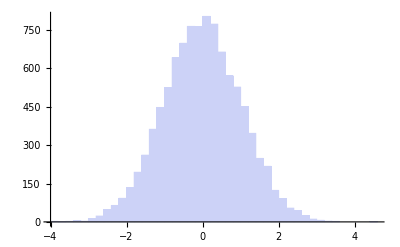

```mathematica
Histogram[Flatten[TrueRandomRealNormal[0,1,{10000}]]]
```

## Ginibre matrix

```mathematica
?TrueGinibreMatrix
```

TrueGinibreMatrix[m,n] returns (m x n)-dimensional complex matrix with entries having real and complex parts distributed according to the normal distribution N[0,1].

```mathematica
TrueGinibreMatrix[10,10]
```

{{-0.202535+0.38923 ⅈ,1.25292+1.05757 ⅈ,1.00025-0.528715 ⅈ,-0.899818+1.675 ⅈ,-0.806214-0.464802 ⅈ,1.5041+0.223994 ⅈ,2.00222+0.0590458 ⅈ,0.982002-0.529819 ⅈ,1.00677+1.2919 ⅈ,-0.347805-1.94535 ⅈ},{-0.160092+0.682932 ⅈ,0.924999-0.02972 ⅈ,-0.212071+2.21664 ⅈ,0.79739+1.06603 ⅈ,-1.26554-0.284471 ⅈ,0.621586-0.258032 ⅈ,1.52413+0.998074 ⅈ,-0.11638+0.701811 ⅈ,0.251758+1.38052 ⅈ,-0.641547-1.14288 ⅈ},{0.525711+0.31421 ⅈ,0.109235-0.658786 ⅈ,0.0948335+0.923732 ⅈ,-0.859974-0.929866 ⅈ,0.251492+0.192945 ⅈ,0.367018-0.835605 ⅈ,-1.11088-0.40073 ⅈ,1.11047+0.366008 ⅈ,0.705104-1.0883 ⅈ,-0.195774-0.511508 ⅈ},{0.0989629-0.683681 ⅈ,0.523322+0.549037 ⅈ,0.107153-0.326959 ⅈ,0.374221-0.326434 ⅈ,-0.04109+1.50035 ⅈ,0.836444-0.336664 ⅈ,0.0904149-1.3154 ⅈ,-0.316788+0.321012 ⅈ,-1.41697+1.2056 ⅈ,-0.130461-0.287813 ⅈ},{-0.327215+0.130512 ⅈ,-0.34285+0.907163 ⅈ,-0.350814+0.0953671 ⅈ,-0.293451-0.119747 ⅈ,-1.15536-0.00972592 ⅈ,0.725762-0.2226 ⅈ,-0.96228-2.03345 ⅈ,0.556795-0.373483 ⅈ,1.12999+0.226281 ⅈ,0.898637+0.744405 ⅈ},{0.167922+0.690975 ⅈ,1.62944-1.11147 ⅈ,1.36071+0.247418 ⅈ,0.17949-1.60451 ⅈ,-0.48485-0.730638 ⅈ,0.278506+0.0211032 ⅈ,-0.5272-0.832501 ⅈ,0.527614-0.924648 ⅈ,1.4176+1.57628 ⅈ,0.186392+1.3418 ⅈ},{-0.720572+1.91063 ⅈ,0.343704+0.794953 ⅈ,1.20304-1.76661 ⅈ,1.79347+0.600778 ⅈ,0.0521501-0.87109 ⅈ,0.0116099-0.196546 ⅈ,1.38691-0.514538 ⅈ,-0.455576+1.95445 ⅈ,1.06967+0.209793 ⅈ,1.04639-0.464589 ⅈ},{0.430768+0.569377 ⅈ,-1.08831-1.35821 ⅈ,0.455276-0.104756 ⅈ,-1.15307-1.77654 ⅈ,1.87621+0.141756 ⅈ,-0.247943+1.39532 ⅈ,-0.33119-0.681218 ⅈ,1.36888-0.379243 ⅈ,-2.04404+1.34721 ⅈ,-0.0393215+0.416662 ⅈ},{0.148875-1.73624 ⅈ,0.13196-0.750822 ⅈ,1.07981+1.00005 ⅈ,-0.357255+0.619889 ⅈ,-0.0208907-0.685237 ⅈ,-0.251751+0.192205 ⅈ,-0.470848+0.389943 ⅈ,-0.20682-0.00729408 ⅈ,0.817046-0.0252863 ⅈ,0.0583673+2.09132 ⅈ},{0.649731+0.626057 ⅈ,3.57009+0.0291149 ⅈ,-1.03179-1.09519 ⅈ,1.12926+0.503509 ⅈ,0.493144-0.107726 ⅈ,-2.37698-1.19024 ⅈ,-1.39576+0.393042 ⅈ,-0.956796+0.172484 ⅈ,1.52965-0.977426 ⅈ,-0.062058+0.127035 ⅈ}}

## Random states - HS measure

```mathematica
statesHS=Table[TrueRandomStateHS[4],{2000}];
```

```mathematica
sortedEvalsHS=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesHS]]ᵀ;
```

```mathematica
masterplotHS=Histogram[{sortedEvalsHS[[1]],sortedEvalsHS[[2]],sortedEvalsHS[[3]],sortedEvalsHS[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15];
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-hs-trqs.pdf",masterplotHS];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-hs-trqs.pdf lambda-prob-hs-trqs.eps"];
```

## Random states - Bures measure

```mathematica
statesBures=Table[TrueRandomStateBures[4],{1000}];
```

```mathematica
sortedEvalsBures=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesBures]]ᵀ;
```

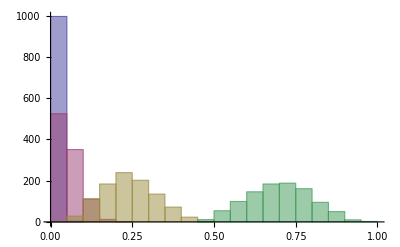

```mathematica
Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]}]
```

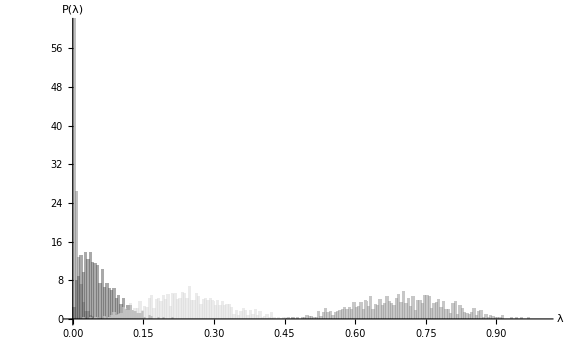

```mathematica
masterplotBures=Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15]
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-bures-trqs.pdf",masterplotBures];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-bures-trqs.pdf lambda-prob-bures-trqs.eps"];
```